# Data Science and Machine Learning

## Lab session 08: Dimensionality Reduction

## Dimensionality Reduction

Objective: represent your original data with fewer features/columns, without distorting the data relationships so much

### Getting started

Let's say you have data points in 3 dimensions:

```mathematica
vectors=Join[RandomReal[{0,3},{1000,3}], RandomReal[{2,5},{1000,3}],RandomReal[{4,7},{1000,3}]];
ListPointPlot3D[vectors]
```

-Graphics3D-

DimensionReduction generates a DimensionReductionFunction that projects data onto a lower-dimensional space.

```mathematica
dr=DimensionReduction[vectors,2]
```

DimensionReducerFunction[…]

The (optional) second argument allows to specify the dimension you are aiming for.
For instance, here we projected our 3-D points into a 2-D space:

```mathematica
reduced = dr[vectors];
ListPlot[reduced]
```

-Graphics-

You can reconstruct the original vectors from the reduced one.
The reconstructed vectors correspond to the original vectors projected on an approximating plane:

```mathematica
reconstructed = dr[reduced, "OriginalVectors"];
ListPointPlot3D[{vectors,reconstructed}]
```

-Graphics3D-

### Application: images

```mathematica
images={-Graphics-,-Graphics-,-Graphics- ,-Graphics-,-Graphics-,-Graphics-};
```

Images are a rectangular grid (list of list) of pixels, and each pixel is a list of numerical values that specifies the color (for instance RGB) or the darkness for black and white pictures. 
Images are thus list of list of list of very large dimensions!

```mathematica
Information[-Graphics-]
FullForm[-Graphics-]
```

Image

Image[NumericArray[List[List[List[3,0,4,255],List[1,0,4,255],List[0,0,4,255],List[0,0,4,255],List[0,0,2,255],129,List[96,75,48,255],List[93,77,51,255],List[93,77,51,255],List[93,77,51,255],List[93,77,51,255]],150,List[1]],""…"8"],3,Rule[1]]
 |  |  |  |

Let's try to reduce the dimensions to a simple 2-dimensional space.

```mathematica
drImages= DimensionReduction[images,2]
```

DimensionReducerFunction[…]

Here is the result of our projection:

```mathematica
imagesPoints = drImages[images]
ListPlot[MapThread[Callout,{imagesPoints,Image[images,ImageSize->40]}]]
```

{{16.6901,0.663878},{8.66663,12.1656},{23.1908,-8.59533},{-14.2674,-21.1947},{-19.8211,-4.78489},{-14.459,21.7455}}

-Graphics-

The dimensionality reduction operation:

saves memory space by compressing data.

allows faster computation (e.g., for prediction or classification tasks), helping to avoid the "curse of dimensionality"

can improve predictor/classifier accuracy by removing noise

Imagine  we want to find the animal from our dataset that looks the more like an image of another animal.
To do so, we can use the Nearest function:

```mathematica
nf = Nearest[imagesPoints -> Automatic]
```

NearestFunction[…]

The function we created ("nf") uses as input the reduced space and returns the position of the nearest element.
If we want to return an image from our original dataset, we can create the following function. 
It is using as input an image, reduces its dimensions, finds the position of the nearest element, and extracts the corresponding image from our original dataset-

```mathematica
nearestanimal[image_] := images[[First@nf[drImages[image]]]]
```

```mathematica
nearestanimal[-Graphics-]
```

-Graphics-

```mathematica
nearestanimal[-Graphics-]
```

-Graphics-

### Application: Fisher's Irises

We will reduce the dimension of the Fisher's Irises dataset in order to visualize it.
The dataset consists of samples from each of three species of iris flowers (setosa, versicolor and virginica). Four features were measured from each flower, the length and the width of the sepal and petal.

```mathematica
iris = ExampleData[{"MachineLearning", "FisherIris"}, "Data"];
RandomSample[iris,5]
```

{{6.2,2.8,4.8,1.8}→virginica,{6.1,3.,4.6,1.4}→versicolor,{6.7,3.1,4.4,1.4}→versicolor,{6.8,3.,5.5,2.1}→virginica,{5.1,3.8,1.9,0.4}→setosa}

We first group the flowers according to their species:

```mathematica
byspecies = GroupBy[iris, Last -> First];
RandomSample[byspecies,1]
```

<|versicolor→{{7.,3.2,4.7,1.4},{6.4,3.2,4.5,1.5},{6.9,3.1,4.9,1.5},{5.5,2.3,4.,1.3},{6.5,2.8,4.6,1.5},{5.7,2.8,4.5,1.3},{6.3,3.3,4.7,1.6},{4.9,2.4,3.3,1.},{6.6,2.9,4.6,1.3},{5.2,2.7,3.9,1.4},{5.,2.,3.5,1.},{5.9,3.,4.2,1.5},{6.,2.2,4.,1.},{6.1,2.9,4.7,1.4},{5.6,2.9,3.6,1.3},{6.7,3.1,4.4,1.4},{5.6,3.,4.5,1.5},{5.8,2.7,4.1,1.},{6.2,2.2,4.5,1.5},{5.6,2.5,3.9,1.1},{5.9,3.2,4.8,1.8},{6.1,2.8,4.,1.3},{6.3,2.5,4.9,1.5},{6.1,2.8,4.7,1.2},{6.4,2.9,4.3,1.3},{6.6,3.,4.4,1.4},{6.8,2.8,4.8,1.4},{6.7,3.,5.,1.7},{6.,2.9,4.5,1.5},{5.7,2.6,3.5,1.},{5.5,2.4,3.8,1.1},{5.5,2.4,3.7,1.},{5.8,2.7,3.9,1.2},{6.,2.7,5.1,1.6},{5.4,3.,4.5,1.5},{6.,3.4,4.5,1.6},{6.7,3.1,4.7,1.5},{6.3,2.3,4.4,1.3},{5.6,3.,4.1,1.3},{5.5,2.5,4.,1.3},{5.5,2.6,4.4,1.2},{6.1,3.,4.6,1.4},{5.8,2.6,4.,1.2},{5.,2.3,3.3,1.},{5.6,2.7,4.2,1.3},{5.7,3.,4.2,1.2},{5.7,2.9,4.2,1.3},{6.2,2.9,4.3,1.3},{5.1,2.5,3.,1.1},{5.7,2.8,4.1,1.3}}|>

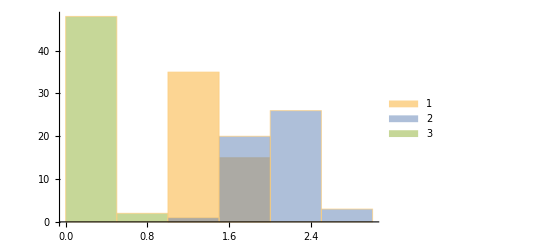

```mathematica
Histogram[{byspecies["versicolor"][[All,4]], byspecies["virginica"][[All,4]],byspecies["setosa"][[All,4]]}, ChartLegends ->{"versicolor", "virginica","setosa" }]
```

#### Principal Component Analysis

The Principal Component Analysis is a linear dimensionality reduction method.
The method works for datasets that have a large number of features and large number of examples; however, the learned manifold can only be linear.

The PCA algorithm in a nutshell:	
    	0. Normalize the features: a) Center each feature, by subtracting the mean; b) Divide by the standard deviation
    	1. Find the direction of the greatest variability (variance). This direction is called the first principal component.
        	2. Find the direction, perpendicular to the 1st component, of the second greatest variability.
            	... Repeat until you found d principal components, with d your number of features.
                Finally, select m<<d components (m is your new dimension) and project your datapoints to the new dimensions.
            
If you are familiar with linear algebra, the principal components (= direction of highest variance) are the eigenvectors of the covariance matrix (between your features). 
Moreover, the variances (of the points projected on the eigenvectors) are the corresponding eigenvalues.
Learn more about why principal components = eigenvectors = greatest variance and why eigenvalues = variances along eigenvector

Let's create a dimension reduction function using all our flowers, reducing the dimension from 4 dimensions (features) to 2 dimensions.
Similarly to when we built predictors and classifiers, you can specify the Method used by the DimensionReduction function.

```mathematica
dirisPCA = DimensionReduction[iris[[All, 1]], 2, Method -> "PrincipalComponentsAnalysis"]
```

DimensionReducerFunction[…]

We now apply the function we just created to our flowers (grouped by species), i.e. we project our points to the 2D space.

```mathematica
byspeciesPCA = dirisPCA /@ byspecies;
```

Finally, we can visualize the result:

```mathematica
ListPlot[Values[byspeciesPCA], PlotLegends -> Keys[byspecies]]
```

-Graphics-

#### Isomap

Isomap stands for isometric mapping. 
It is a nonlinear neighbor-based dimensionality reduction method, which attempts to find a low-dimensional embedding of data via a transformation that preserves geodesic distances.
Isomap is able to learn nonlinear manifolds; however, it gives poor results on boundaries, can fail if data has high-density variations, and is computationally expensive.

Isomap algorithm in a nutshell:
	1. Find the k neareast neighbors of every data point (k is a parameter that can be selected).
    	2. Construct the neighborhood graph: points are connected only if they are each other neighbors.
        	3. Compute the shortest path between each pair of data points, i.e. find the "geodesic distance". This gives you a matrix of graph distances.
            	4. Find a set of coordinates (x1, x2, ..., xN) that minimize the "stress":

If you want to learn more.

As before, we build our Dimension Reduction function, specifying the "Isomap" Method, then apply it, and visualize the results:

```mathematica
dirisISO = DimensionReduction[iris[[All, 1]], 2, Method -> "Isomap"];
byspeciesISO = dirisISO /@ byspecies;
ListPlot[Values[byspeciesISO], PlotLegends -> Keys[byspecies]]
```

-Graphics-

As option, you can specify the number of nearest neighbors that should be used:

```mathematica
dirisISOnn = DimensionReduction[iris[[All, 1]], 2, Method -> {"Isomap", "NeighborsNumber"->10}];
byspeciesISOnn = dirisISOnn /@ byspecies;
ListPlot[Values[byspeciesISOnn], PlotLegends -> Keys[byspecies]]
```

-Graphics-

#### t-SNE

t-SNE stands for t-distributed Stochastic Neighbor Embedding.
It is a nonlinear non-parametric dimensionality reduction method, which attempts to learn a low-dimensional representation of the data that preserves the local structure of the data.
t-SNE works for datasets with nonlinear manifolds and is particularly suited for the visualization of high-dimensional datasets; however, it is slow to train for datasets that have a large number of features and large number of examples.

t-SNE algorithm in a nutshell:
	1. Find the similarities between data points. 
    	The similarity between datapoint x_i and datapoint x_j is the conditional probability that x_j would pick x_j as its neighbor, when you take a Gaussian distribution centered at x_i.
            
    			   	where ϵ  corresponds to a neighborhood radius (variance) = perplexity.
                 2. Find the lower-dimensional datapoints y_i such the similarities in the lower-dimensional space q_ij match the original one p_ij
                 The similarities in the lower-dimensional space are given by:
			             
                As before, the similarities are the conditional probabilities that  y_i would pick y_j as its neighbor. However, this time we are using a Student t-distribution because the Gaussian creates what is called a "crowding problem"
    
Explanation of the t-SNE algorithm

As before, we build our Dimension Reduction function, specifying the "TSNE" Method, then apply it, and visualize the results:

```mathematica
dirisTSNE = DimensionReduction[iris[[All, 1]], 2, Method -> "TSNE"];
byspeciesTSNE = dirisTSNE /@ byspecies;
ListPlot[Values[byspeciesTSNE], PlotLegends -> Keys[byspecies]]
```

-Graphics-

As option, you can define the "Perplexity", i.e. the neighborhood radius.

```mathematica
dirisTSNEp = DimensionReduction[iris[[All, 1]], 2, Method ->{ "TSNE", "Perplexity"->10}];
byspeciesTSNEp = dirisTSNEp /@ byspecies;
ListPlot[Values[byspeciesTSNEp], PlotLegends -> Keys[byspecies]]
```

-Graphics-

### Application: Swiss roll

We want to reduce the dimension of the Swiss roll from 3D to 2D.
We will compare the performance of the previously seen methods.

```mathematica
swissRoll = Table[ Insert[AngleVector[1 + {2, 8}*RandomReal[]], RandomReal[], 2], 1000];
```

```mathematica
ListPointPlot3D[swissRoll, BoxRatios -> {1, 1, 1}]
```

-Graphics3D-

Let's first create our dimension reduction projection.

```mathematica
swissRollPCA = DimensionReduction[swissRoll, 2, Method -> "PrincipalComponentsAnalysis"];
swissRollISO = DimensionReduction[swissRoll, 2, Method -> "Isomap"];
swissRollTSNE = DimensionReduction[swissRoll, 2, Method -> "TSNE"];
```

We apply our projection:

```mathematica
swissRollPCAreduced = swissRollPCA[swissRoll];
swissRollISOreduced =  swissRollISO[swissRoll];
swissRollTSNEreduced =  swissRollTSNE[swissRoll];
```

We can now visualize the results in the reduced space:

```mathematica
Grid[{{"PCA", "Isomap", "TSNE"}, 
{ListPlot[Style[#, Hue[First[#]/10]] & /@ swissRollPCAreduced, AspectRatio -> 1/2, PlotStyle -> Directive[PointSize -> Small]],
ListPlot[Style[#, Hue[First[#]/20]] & /@ swissRollISOreduced, AspectRatio -> 1/2, PlotStyle -> Directive[PointSize -> Small]],
ListPlot[Style[#, Hue[First[#]/60]] & /@ swissRollTSNEreduced, AspectRatio -> 1/2, PlotStyle -> Directive[PointSize -> Small]] }}]
```

PCA | Isomap | TSNE
-Graphics- | -Graphics- | -Graphics-

We can also visualize the dataset in the original space, with each point colored according to its reduced variable:

```mathematica
Grid[{{"PCA", "Isomap", "TSNE"},
{ListPointPlot3D[Style[#, Hue[First[swissRollPCA[#]]/10]] & /@ swissRoll, BoxRatios -> {1, 1, 1}],
ListPointPlot3D[Style[#, Hue[First[swissRollISO[#]]/20]] & /@ swissRoll, BoxRatios -> {1, 1, 1}],
ListPointPlot3D[Style[#, Hue[First[swissRollTSNE[#]]/60]] & /@ swissRoll, BoxRatios -> {1, 1, 1}]}}]
```

PCA | Isomap | TSNE
-Graphics3D- | -Graphics3D- | -Graphics3D-

What is the best approach? Why?

## Useful links

Introduction to WL: Machine Learning

Machine Learning functions